## Introduction

Code used in paper “Collective behaviour of swarmalators on a 1D ring”

## Main

### Dynamic simulation

```mathematica
(*Preamble*)
{dt,n,T}={0.25,200,500}; 
{J,k}={1,-5};
{e,b}={3,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
results=plotResults[znew,pin]
]
```

$Aborted

### Static simulation

#### Simulation

```mathematica
(*Preample*)
{dt,n,T}={0.5,100,100}; 
{J,k}={40,-42};   
{Ex,Eθ} = {0,0};
{b1,b2} = {1,1};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
{Wps,Wms}={{},{}};
ts={};

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
{Wp,Wm}=findWs[znew];AppendTo[ts,dt*t];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
]
```

#### Plots

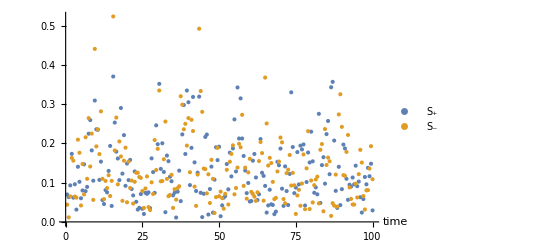

```mathematica
ListPlot[{{ts,Wps//Abs}ᵀ,{ts,Wms//Abs}ᵀ},AxesLabel->{Style["time",13]},PlotLegends->{"S_+","S_-"}]
```

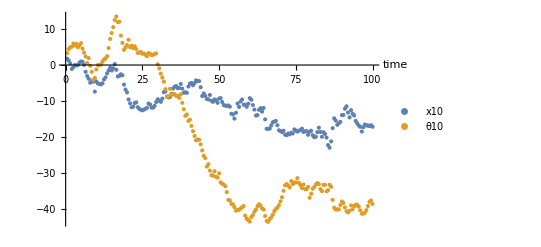

```mathematica
swarmalatorIndex=10;
ListPlot[{{ts,xs[[All,swarmalatorIndex]]}ᵀ,{ts,θs[[All,swarmalatorIndex]]}ᵀ},AxesLabel->{Style["time",13]},
PlotLegends->{"x"<>ToString[swarmalatorIndex],"θ"<>ToString[swarmalatorIndex]}]
```

```mathematica
(*Manipulate[ListPlot[{xs[[t,All]]//mod,θs[[t,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}],{t,1,Dimensions[xs][[2]],1}]*)
```

## Catalog states: E = 0

### Pure sync

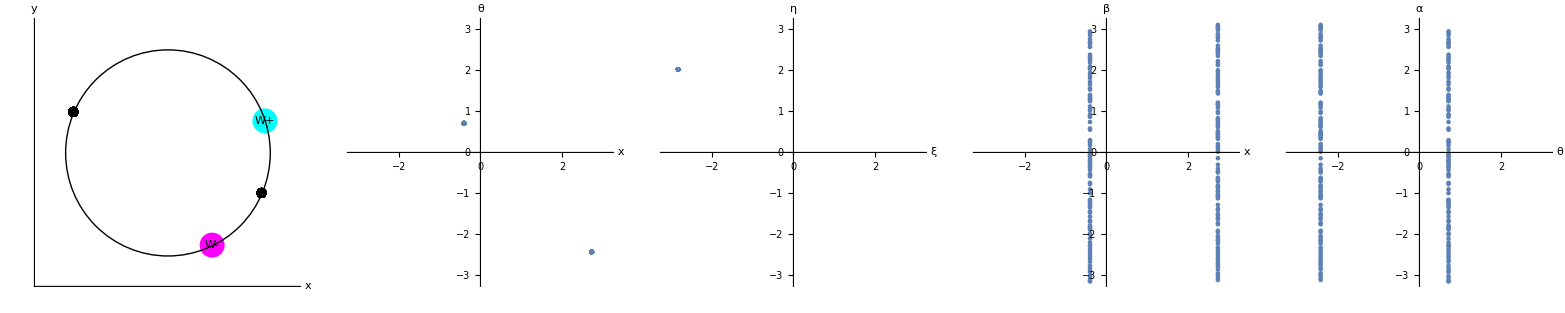

```mathematica
(*Preamble*)
{dt,n,T}={0.25,200,50}; 
{J,k}={1,2};

{Ex,Eθ} = {0,0};
b=0;
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Partial sync

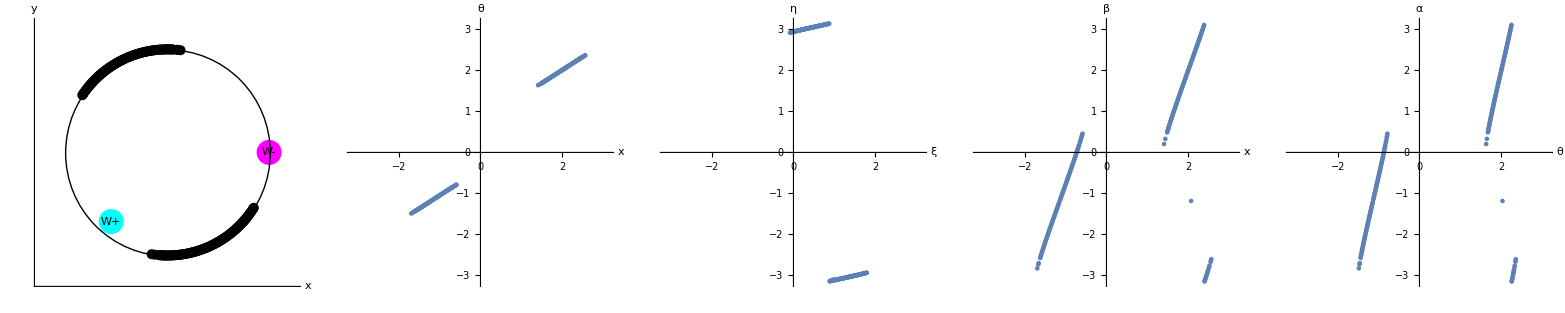

```mathematica
(*Preamble*)
{dt,n,T}={0.25,200,100}; 
{J,k}={1,2};

{Ex,Eθ} = {0,0};
b=0.5;
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Double phase wave

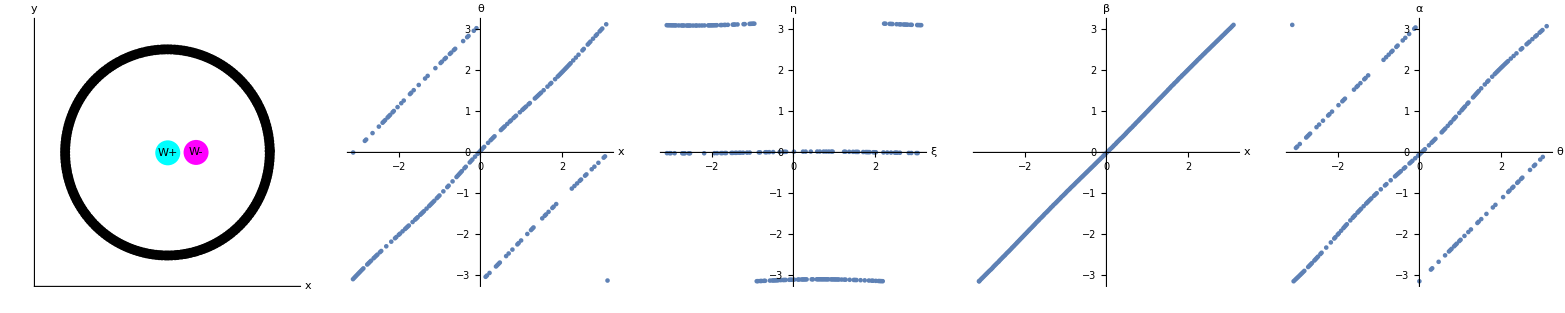

```mathematica
(*Preamble*)
{dt,n,T}={0.5,200,200}; 
(*{J,k}={1,1}; *)  (*Static sync / π state, depending on IC*)
(*{J,k}={1,-0.5};*) (*Static phase wave*)
(*{J,k}={1,-1.05};*) (*Active async*)
(*{J,k}={1,-3};*) (*Static async*)
{J,k}={1,-2};

{Ex,Eθ} = {0,0};
b=0.3;
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Phase wave

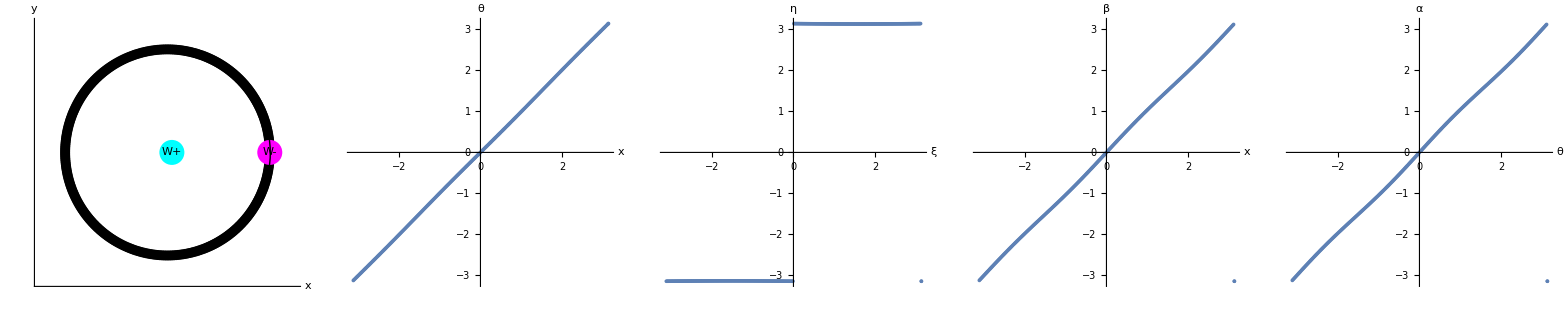

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,2};
{e,b}={0,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

## Catalog states: E > 0

### Traveling loops

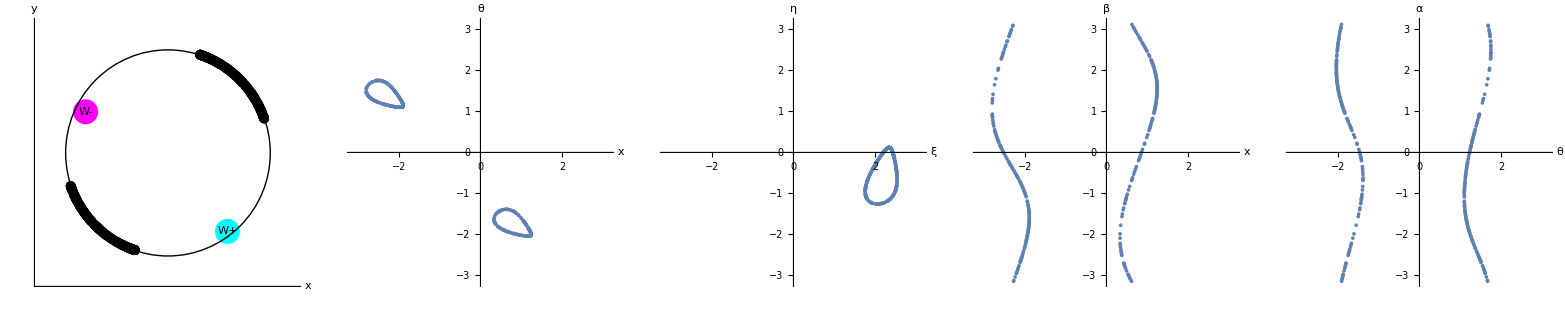

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,2};
{e,b}={1.5,0.75};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Messy waves

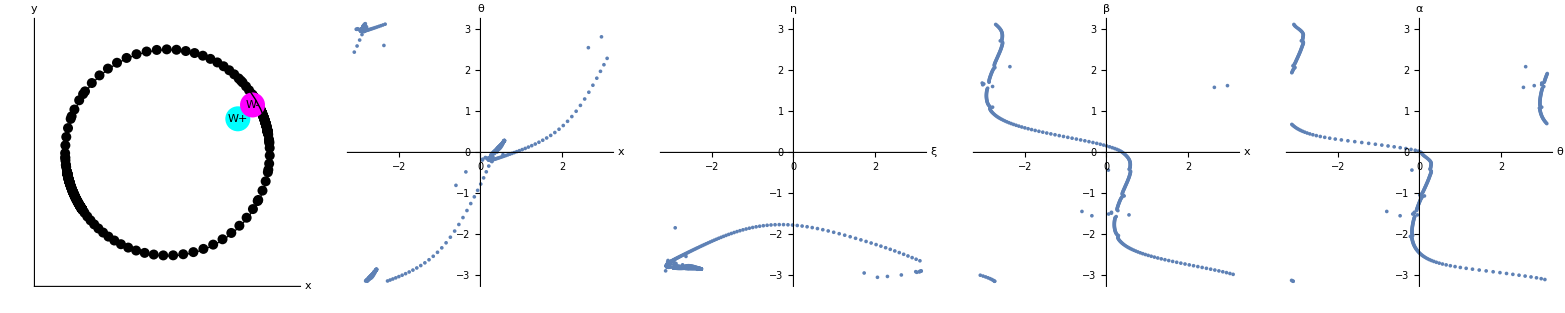

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,2};
{e,b}={2.2,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Sliding phase waves -- further investigate here

The transients look a bit like a chimera here -- so watch in movie.

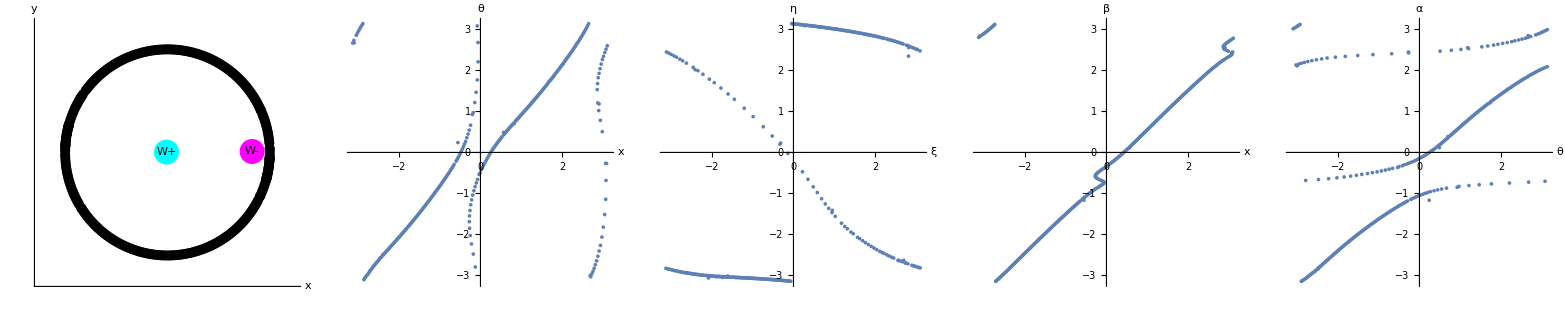

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,-5};
{e,b}={0.9,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Noisy phase wave

Here the wave in (x,β) space breathes

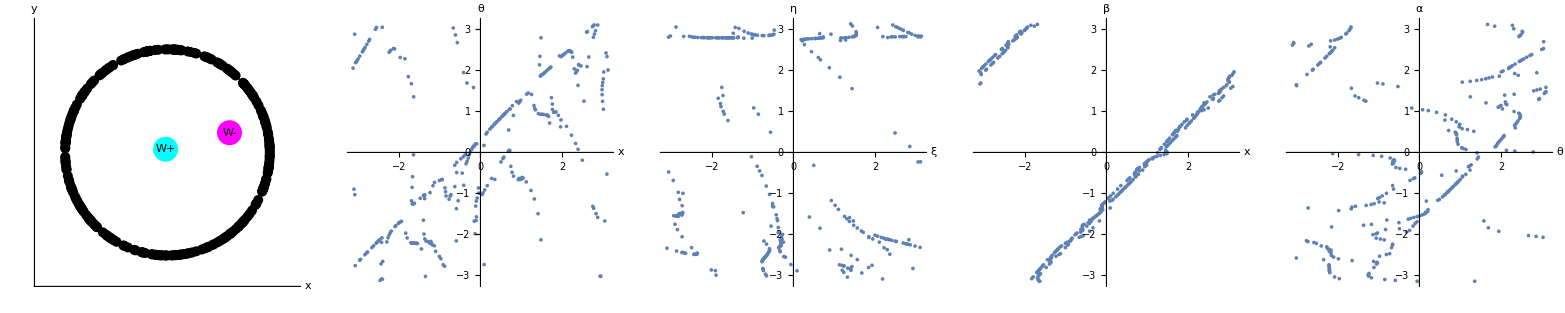

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,-5};
{e,b}={1.9,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

### Bursty async

Here the wave in (x,β) space bursts and rotates.

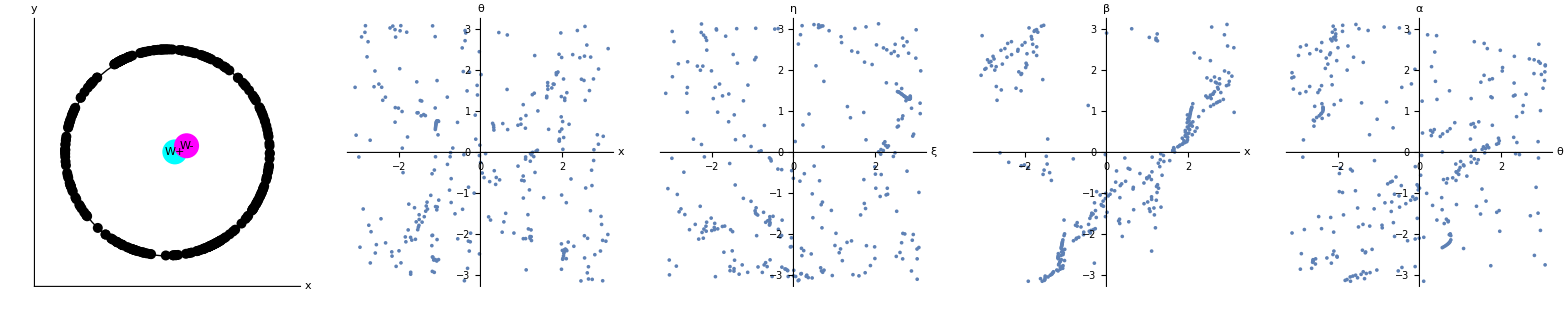

```mathematica
(*Preamble*)
{dt,n,T}={0.5,300,200}; 
{J,k}={1,-5};
{e,b}={2.5,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
]
plotResults[znew,pin]
```

## S(K): E = 0

### b = 0

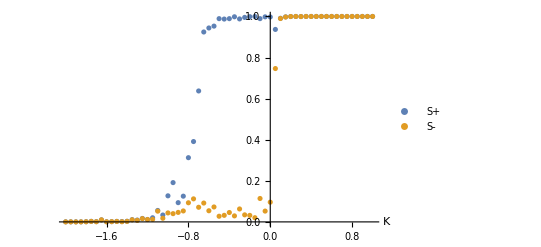

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,50}; 
{J,k}={1,k1};
{Ex,Eθ} = {0,0};
b=0;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-2,1,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

### b = 0.1

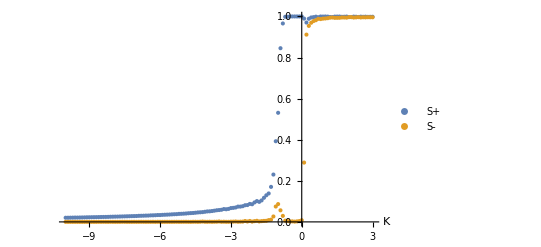

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,100}; 
{J,k}={1,k1};
{Ex,Eθ} = {0,0};
b=0.1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,3,0.1}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

### b = 0.2

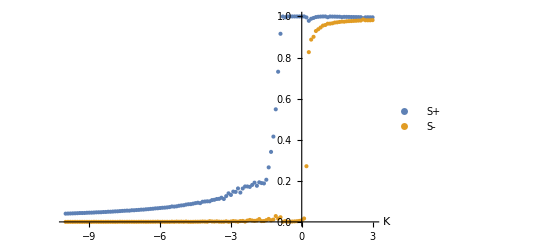

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,100}; 
{J,k}={1,k1};
{Ex,Eθ} = {0,0};
b=0.2;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k1,Sp,Sm},
{k1,-10,3,0.1}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"K"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

## S(b): E = 0

### K = 2

```mathematica
data1=ParallelTable[
{dt,n,T}={0.5,200,200}; 
{J,k}={1,2};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,-1.5,1.5,0.025}
];
```

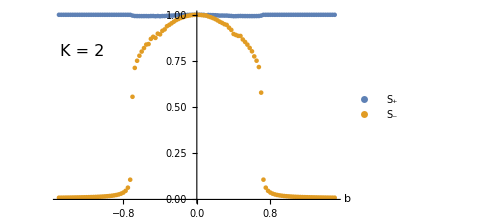

figures/order-pars-versus-b-K2.png

```mathematica
p1=ListPlot[{data1[[All,{1,2}]],data1[[All,{1,3}]]},AxesLabel->{Style["b",25,Italic]},PlotLegends->{Style["S_+",17,Italic],Style["S_-",17,Italic]},AxesStyle->15,Epilog->{Text[Style["K = 2",16,Italic],{-1.25,0.8}]},ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-versus-b-K2.png",p1]
```

### K = -0.5

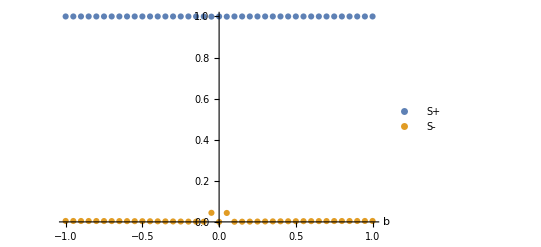

```mathematica
data=ParallelTable[
{dt,n,T}={0.5,200,200}; 
{J,k}={1,-0.5};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.5Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,-1,1,0.05}
];
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},AxesLabel->{"b"},PlotLegends->{"S+","S-"},AxesStyle->15]
```

### K = -5

```mathematica
data2=ParallelTable[
{dt,n,T}={0.5,300,200}; 
{J,k}={1,-5};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.8Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,-5,5,0.025}
];
```

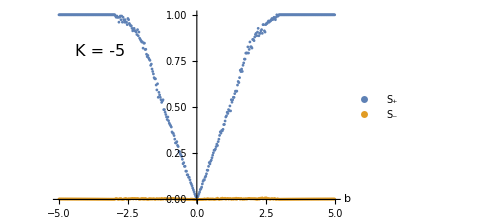

```mathematica
p2=ListPlot[{data2[[All,{1,2}]],data2[[All,{1,3}]]},AxesLabel->{Style["b",25,Italic]},PlotLegends->{Style["S_+",17,Italic],Style["S_-",17,Italic]},AxesStyle->15,Epilog->{Text[Style["K = -5",16,Italic],{-3.5,0.8}]},ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/order-pars-versus-b-Km5.png",p2];
```

### Plot together

```mathematica
pAll=Grid[{{p1,p2}}]
Export["figures/order-pars-together.png",pAll];
```

-Graphics- | -Graphics-

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];
```